```mathematica
Subscript[h, 1][ν_, x_] := Sqrt[π]/2 HankelH1[ν, x]
```

```mathematica
Subscript[h, 2][ν_, x_] := Sqrt[π]/2 HankelH2[ν, x]
```

```mathematica
f[a_, ν_] := 204/π^2 1/a NIntegrate[ξ Sin[ξ/102 a]*Abs[Subscript[h, 1][ν, ξ a]*Subscript[h, 2][ν, ξ a]]*(Im[Subscript[h, 1][ν,ξ]*Subscript[h, 2][ν,ξ*a]])^2, {ξ, 0,∞}]
```

General::munfl: Exp[-2274.63] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.13614×10^-31 4.74312×10^-278 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.86464×10^-31 1.22091×10^-278 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

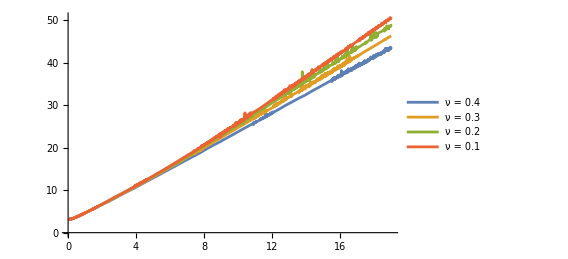

```mathematica
Plot[{-Log[f[Exp[t], 0.4]],-Log[f[Exp[t], 0.3]],-Log[f[Exp[t], 0.2]],-Log[f[Exp[t], 0.1]]}, {t, Log[1.05], 19},PlotLegends->{"ν = 0.4","ν = 0.3","ν = 0.2","ν = 0.1"}]
```

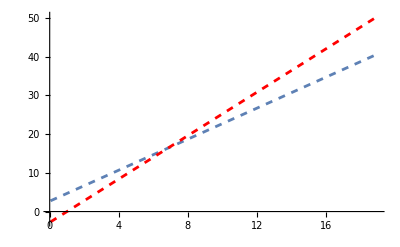

```mathematica
Plot[{2(t-1.96)+6.6, 2.8(t-18.86)+50}, {t,Log[1.05],19}, PlotStyle->{{Dashed},{Dashed, Red}}]
```

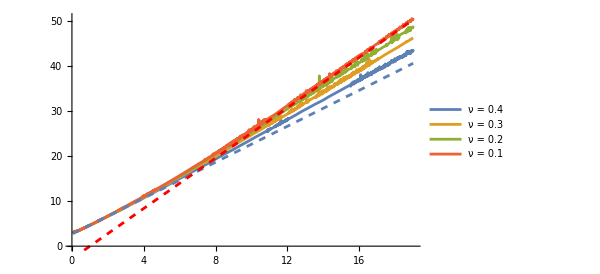

```mathematica
Show[Out[4],Out[5]]
```